```mathematica
Needs["HierarchicalClustering`"]
SetOptions[{Plot,MatrixPlot},ImageSize->350{1,1}];
```

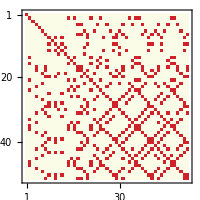
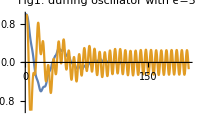
-Graphics- -Graphics- -Graphics-

```mathematica
Module[{tmax=200,ϵ,δ=4,γ,μ=60,T1,T2},
ϵ=1;γ=2;
T1=1;T2=1;
nlo1=NDSolveValue[{μ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t/T1],y[0]==1,y'[0]==0},y,{t,0,tmax}];
ϵ=10;γ=15;
nlo2=NDSolveValue[{μ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t/T1],y[0]==1,y'[0]==0},y,{t,0,tmax}];
Plot[{nlo1[t],nlo2[t]},{t,0.,tmax},PlotLabel->"Fig1. duffing oscillator with ϵ=5",PlotRange->{{0,tmax},{-1,1}},PlotLegends->{"ϵ=5"}]

With[{stepSize=4,end=tmax,nn=0.005},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]MatrixPlot[UnitStep[nn-DistanceMatrix[nlo2[Range[0,end,stepSize]]]],ColorFunction->"TemperatureMap"]
]
]
```

NDSolveValue::dvnoarg: The function T2$14397 appears with no arguments.

NDSolveValue::dsvar: 0.00122571 cannot be used as a variable.

NDSolveValue::dsvar: 1.22572 cannot be used as a variable.

General::stop: Further output of NDSolveValue :: dsvar will be suppressed during this calculation.

NDSolveValue::dvnoarg: The function T2$14397 appears with no arguments.

DistanceMatrix::list: List expected at position 1 in NDSolveValue[{y[t] + 20 y[« 1 »]^3 + 6 SuperscriptBox[.

MatrixPlot::mat0: Argument 0.001`  - DistanceMatrix[NDSolveValue[{y[« 1 »] + Times[« 2 »] + Times[« 2 »] + SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »] == Cos[Times[« 2 »]], y[0] == 1, SuperscriptBox[ at position 1 is not a matrix.

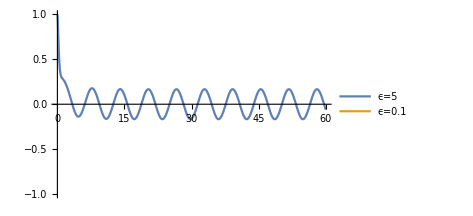
-Graphics- -Graphics- MatrixPlot[UnitStep[0.001-DistanceMatrix[NDSolveValue[{y[t]+20 y[t]^3+6 y'[t]+y''[t]==Cos[t/T2$14397],y[0]==1,y'[0]==0,T2$14397[0]==1,WhenEvent[t>20,T2$14397[t]→5 T2$14397[t]]},y,{t,0,60},DiscreteVariables→T2$14397][{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.,20.5,21.,21.5,22.,22.5,23.,23.5,24.,24.5,25.,25.5,26.,26.5,27.,27.5,28.,28.5,29.,29.5,30.,30.5,31.,31.5,32.,32.5,33.,33.5,34.,34.5,35.,35.5,36.,36.5,37.,37.5,38.,38.5,39.,39.5,40.,40.5,41.,41.5,42.,42.5,43.,43.5,44.,44.5,45.,45.5,46.,46.5,47.,47.5,48.,48.5,49.,49.5,50.,50.5,51.,51.5,52.,52.5,53.,53.5,54.,54.5,55.,55.5,56.,56.5,57.,57.5,58.,58.5,59.,59.5,60.}]]],ColorFunction→Monochrome]

```mathematica
Module[{tmax=60,ϵ,δ=6,γ=1,μ=1,T1,T2},
ϵ=20;
T1=1;
nlo1=NDSolveValue[{μ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t/T1],y[0]==1,y'[0]==0},y,{t,0,tmax}];
ϵ=20;
NDSolveValue[{μ y''[t]+δ y'[t]+y[t]+ϵ (y[t])^3==γ Cos[t/T2[t]],y[0]==1,y'[0]==0,T2[0]==1,WhenEvent[t>20,T2[t]->5*T2[t]]},y,{t,0,tmax},DiscreteVariables->T2];

Plot[{nlo1[t],nlo2[t]},{t,0.,tmax},PlotRange->{{0,tmax},{-1,1}},PlotLegends->{"ϵ=5","ϵ=0.1"}]
With[{stepSize=0.5,end=tmax,nn=0.001},
MatrixPlot[UnitStep[nn-DistanceMatrix[nlo1[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]

MatrixPlot[UnitStep[nn-DistanceMatrix[nlo2[Range[0,end,stepSize]]]],ColorFunction->"Monochrome"]
]
]
```